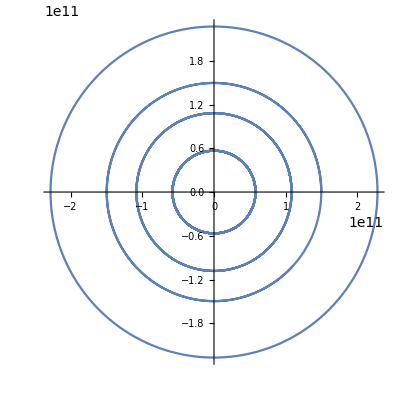

```mathematica
mercuryX[t_]=QuantityMagnitude[mercurySemiMajorAxis]*Cos[t/QuantityMagnitude[mercuryOrbitEarthYears]];
mercuryY[t_]=QuantityMagnitude[mercurySemiMinorAxis]*Sin[t/QuantityMagnitude[mercuryOrbitEarthYears]];
mercuryPlotXY=ParametricPlot[{mercuryX[t],mercuryY[t]},{t,0,marsOrbitEarthYears*2Pi}];
venusX[t_]=QuantityMagnitude[venusSemiMajorAxis]*Cos[t/QuantityMagnitude[venusOrbitEarthYears]];
venusY[t_]=QuantityMagnitude[venusSemiMinorAxis]*Sin[t/QuantityMagnitude[venusOrbitEarthYears]];
venusPlotXY=ParametricPlot[{venusX[t],venusY[t]},{t,0,marsOrbitEarthYears*2Pi}];
earthX[t_]=QuantityMagnitude[earthSemiMajorAxis]*Cos[t/QuantityMagnitude[earthOrbitEarthYears]];
earthY[t_]=QuantityMagnitude[earthSemiMinorAxis]*Sin[t/QuantityMagnitude[earthOrbitEarthYears]];
earthPlotXY=ParametricPlot[{earthX[t],earthY[t]},{t,0,marsOrbitEarthYears*2Pi}];
marsX[t_]=QuantityMagnitude[marsSemiMajorAxis]*Cos[t/QuantityMagnitude[marsOrbitEarthYears]];
marsY[t_]=QuantityMagnitude[marsSemiMinorAxis]*Sin[t/QuantityMagnitude[marsOrbitEarthYears]];
marsPlotXY=ParametricPlot[{marsX[t],marsY[t]},{t,0,marsOrbitEarthYears*2Pi}];
Show[{mercuryPlotXY,venusPlotXY,earthPlotXY,marsPlotXY},PlotRange->All]
```

```mathematica
animatedMercuryOrbit=Animate[Show[mercuryPlotXY,Graphics[{PointSize[0.02],Point[{mercuryX[t],mercuryY[t]}]}]],{t,0,marsOrbitEarthYears*2Pi}];
animatedVenusOrbit=Animate[Show[venusPlotXY,Graphics[{Pink,PointSize[0.02],Point[{venusX[t],venusY[t]}]}]],{t,0,marsOrbitEarthYears*2Pi}];
animatedEarthOrbit=Animate[Show[earthPlotXY,Graphics[{Blue,PointSize[0.02],Point[{earthX[t],earthY[t]}]}]],{t,0,marsOrbitEarthYears*2Pi}];
animatedMarsOrbit=Animate[Show[marsPlotXY,Graphics[{Red,PointSize[0.02],Point[{marsX[t],marsY[t]}]}]],{t,0,marsOrbitEarthYears*2Pi}];
animatedOrbitsXY=Animate[Show[{mercuryPlotXY,Graphics[{PointSize[0.02],Point[{mercuryX[t],mercuryY[t]}]}],venusPlotXY,Graphics[{Pink,PointSize[0.02],Point[{venusX[t],venusY[t]}]}],earthPlotXY,Graphics[{Blue,PointSize[0.02],Point[{earthX[t],earthY[t]}]}],marsPlotXY,Graphics[{Red,PointSize[0.02],Point[{marsX[t],marsY[t]}]}]},PlotRange->All],{t,0,marsOrbitEarthYears*2Pi}]
```